## Expressions (10 min)

## Expressions

Everything in the Wolfram Language is an expression

head[arg_1,arg_2,...,arg_n]

arg_1 : head_1[arg_(1,1),arg_(1,2),...,arg_(1,n_1)]

arg_2: head_2[arg_(2,1), arg_(2,2),...,arg_(2,n_2)]

⋮

arg_n: head_2[arg_(n,1), arg_(n,2),...,arg_(n,n_n)]

## Atomic Elements

These can be though of as the basic types of elements in the Wolfram Language. They include

Integer

```mathematica
{1,2,3,4,-1,-2,-3,..}
```

Real

```mathematica
{3.4,2.0,9.123456,...}
```

String

```mathematica
{"Hello","Welcome to day 2 of the Wolfram Workshop!", "xadsasvasd",...}
```

Rational

```mathematica
{1/2,3/4,4/5,16/3,...}
```

Symbol

```mathematica
{x, Pi, π, hello, Plot,...}
```

We can identify which constructs are atoms by using the AtomQ function.

```mathematica
(*Examples*){AtomQ[1],AtomQ[3.4],AtomQ["Hello"],AtomQ[1/2],AtomQ[x]}
```

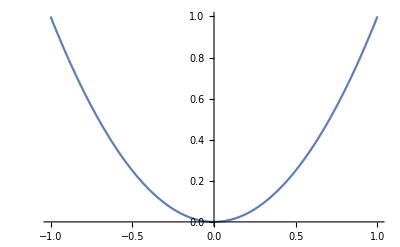
```mathematica
(*Non-Examples*){AtomQ[2x],AtomQ[5 x^2+6x+1==0],AtomQ[{1,2,3}],AtomQ[LinguisticAssistant],AtomQ[-Graphics-]}
```

This tells you that these last expressions are something more complicated (we will get to that later).

We can tell what “type” of atomic elements we have by using the Head function.

```mathematica
{Head[1],Head[3.4],Head["Hello"],Head[1/2],Head[x]}
```

## More complex expressions

What about the non-atomic expressions that we had before?

We can still take the Head of any expression.

```mathematica
{Head[2x],Head[5 x^2+6x+1==0],Head[{1,2,3}],Head[LinguisticAssistant],Head[-Graphics-]}
```

Even though they look all different, internally they all have the same structure, that comes from language design principles in logic. That is, they all have the form:

head[argument1, argument2,...]

where the heads are Times, Equal, List, Entity, and Graphics respectively, and each argument could be either another complex expression or an atomic element.

head[arg_1,arg_2,...,arg_n]

arg_1 : head_1[arg_(1,1),arg_(1,2),...,arg_(1,n_1)]

arg_2: head_2[arg_(2,1), arg_(2,2),...,arg_(2,n_2)]

⋮

arg_n: head_2[arg_(n,1), arg_(n,2),...,arg_(n,n_n)]

We can see in detail how these expressions are understood by the software using the FullForm function

```mathematica
FullForm[2x]
```

```mathematica
FullForm[5 x^2+6x+1==0]
```

```mathematica
FullForm[{1,2,3}]
```

```mathematica
FullForm[LinguisticAssistant]
```

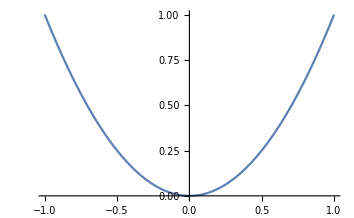
```mathematica
FullForm[-Graphics-]
```

Two other common “Form” functions are InputForm and FullForm

```mathematica
(*TODO I added a phrase up here*)
```

```mathematica
{InputForm[2x],InputForm[5 x^2+6x+1==0],InputForm[{1,2,3}],InputForm[LinguisticAssistant]}
```

```mathematica
{TreeForm[2x],TreeForm[5 x^2+6x+1==0],TreeForm[{1,2,3}],TreeForm[LinguisticAssistant]}
```

## An Important Observation about Head

Even though Head gives you the type of element we are working with, it should not be confused with the Function that led to its creation.

```mathematica
{Table[i,{i,5}],
Range[5],
List[1,2,3,4,5],
Map[Length,{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}]}
```

```mathematica
Head/@{Table[i,{i,5}],
Range[5],
List[1,2,3,4,5],
Map[Length,{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}]}
```

## Why is understanding expressions important

Everything is an expression

The notebook I am presenting with, the cells, the code itself

To understand the language and different constructs as they appear.

Knowing that there is a carefully thought structuring of the language helps you get familiar with new functionality as you run into it.

To be able to read code from others(and eventually modify it for your own purposes)

Even though there is a standard form (FullForm) of expressions there are different ways in which code can be input.

f@a

a//f

f[a]

## Functions that work with all Expressions

Head

Head[atomic] gives you the type of atomic element.

head[f[e1,e2,...,en]] gives you f.

Length

Length of an atomic element gives you 0.

```mathematica
Length["Hello There"]
```

```mathematica
(*TODO placeholder breakdown*)
```

Length  of f[e1,e2,..en] gives you n.

```mathematica
Length[{1,2,3,4}]
```

```mathematica
Length[a+2x y]
```

```mathematica
Length[2x y]
```

```mathematica
(*TODO changed placeholders to input*)
```

```mathematica
Length[If[a<b,"x","y"]]
```

```mathematica
Length[If[2<3,"x","y"]]
```

Part

```mathematica
Part[expr,i]
```

Part[expr,0] is the same as taking Head[expr]

Part[f[e1,e2,...,en],k] is the same as ek.

We usually use the shorthand expr[[k]] for Part[expr,k]

```mathematica
{1,2,3,4}[[2]]
```

```mathematica
{1,2,3,4}[[0]]
```

```mathematica
3[[0]]
```

```mathematica
x[[0]]
```

```mathematica
(*TODO changed placeholders to input*)
```

```mathematica
x[[1]]
```

```mathematica
{1,2,3,4}[[5]]
```

```mathematica
a+b[[2]]
```

```mathematica
(a+b)[[2]]
```

```mathematica
(*TODO changed placeholders to input*)
```

## Exercises

For the following questions consider the following 9 expressions

```mathematica
Grid[Partition[{5,{1,2},m,Select,x+3,"\"{1,2,3}\"",HoldForm[1+7],Log[7],HoldForm[Log[7.]]},3],Frame->All]
```

```mathematica
(*TODO ran the code so we would get the Grid, rolled back the code*)
```

Which expressions are atomic?

```mathematica
AtomQ[1+7]
```

```mathematica
AtomQ[Log[7]]
```

```mathematica
AtomQ[Log[7.0]]
```

```mathematica
Log[7.0]
```

What are the heads of the expressions?

What are the lengths of each of the expressions?

Can the second Part of an expression be a List?

```mathematica
{a,{a,b}}[[2]]
```

## Assignments (10 min)

## Assignment in the Wolfram Language

```mathematica
x=y
```

```mathematica
y:=z
```

```mathematica
f[]=expr
```

```mathematica
f[x_,y_]:=expr2
```

## Immediate Assignment vs Delayed Assignment

There are two main operations that are commonly used for assignment(i.e. giving values to variables and other Symbols by the user). These two functions are Set(=) and SetDelayed(:=)

Set[var,expr] (var=expr) immediately assigns the value of expr to var.

```mathematica
x=34
```

```mathematica
x+4
```

```mathematica
y=x
```

```mathematica
Graphics[{Text[Framed["x"],{0,0}],Arrow[{{0,0},{.5,0}},.1],Text[Framed[34],{.5,0}],
Text[Framed["y"],{0,-.25}],Arrow[{{0,-.25},{.5,0}},.1]},ImageSize->Small]
```

```mathematica
(*TODO rolled back the code*)
```

```mathematica
y+4
```

```mathematica
x=12
```

```mathematica
y+4
```

```mathematica
Graphics[{Text[Framed["x"],{0,0}],Arrow[{{0,0},{.5,0.25}},.1],
Text[Framed[12],{.5,0.25}],Text[Framed[34],{.5,0}],
Text[Framed["y"],{0,-.25}],Arrow[{{0,-.25},{.5,0}},.1]},ImageSize->Small]
```

```mathematica
(*TODO rolled back the code*)
```

SetDelayed[var,expr] (var:=expr) makes it so that every time that var is called later in the file, then expr called and run to produce a value in the place of var.

```mathematica
x=34
```

```mathematica
y:=x
```

```mathematica
Graphics[{Text[Framed["x"],{0,0}],Arrow[{{0,0},{.5,0}},.1],Text[Framed[34],{.5,0}],
Text[Framed["y"],{0,-.25}],Arrow[{{0,-.25},{0,0}},.05]},ImageSize->Small]
```

```mathematica
(*TODO rolled back the code*)
```

```mathematica
y+4
```

```mathematica
x=12
```

```mathematica
y+4
```

```mathematica
Graphics[{Text[Framed["x"],{0,0}],Arrow[{{0,0},{.5,0.25}},.1],
Text[Framed[12],{.5,0.25}],Text[Framed[34],{.5,0}],
Text[Framed["y"],{0,-.25}],Arrow[{{0,-.25},{0,0}},.05]},ImageSize->Small]
```

```mathematica
(*TODO rolled back the code*)
```

## Function assignment

We can create functions with no arguments

```mathematica
constantSix[]=6
```

Functions with a dummy argument

```mathematica
constSix[_]=6
```

```mathematica
constSix[2324]
```

If we want to use the parameter in the definition of the function we need to give it a name

```mathematica
identity[z_]=z
```

```mathematica
{identity[56],identity[hello],identity[10]}
```

It works, but in Wolfram Language, unless you are not careful the above can result in an issue

```mathematica
y=3;
```

```mathematica
square[y_]=y^2
```

```mathematica
{square[5],square[hello],square[10]}
```

The “correct” way would be using the SetDelayed function.

```mathematica
cube[y_]:=y^3
```

```mathematica
{cube[56],cube[hello],cube[10]}
```

## Information on values

Symbols that have not been referred to at all will throw out Missing object

```mathematica
?bye
```

```mathematica
?
```

You can also use Information to get information about Built-In symbols

```mathematica
Information[Plot]
```

```mathematica
Information[cube]
```

They look a bit different as they carry templates, options, attributes, and are stored in the System` context.
For example, they all have the Protected attribute which prevents them from being overwritten

```mathematica
Plot=23
```

Adding options, attributes and other properties to user defined functions is possible  but we will only see the tip of the iceberg on that in this lecture

## Names[“Global`*”]

We can check what are the symbols that we as the user have created by using the Names function

```mathematica
Names["Global`*"]
```

We can use this to build a dashboard with definitions

```mathematica
Grid[{#,If[NumericQ[ToExpression[#]],ToExpression[#],DownValues[Evaluate[ToExpression[#]]]]}&/@Names["Global`*"],Frame->All]
```

```mathematica
{{"a", {}}, {"b", {}}, {"c", {}}, {"constantSix", {HoldPattern[constantSix[]]:>6}}, {"constSix", {HoldPattern[constSix[_]]:>6}}, {"cube", {HoldPattern[cube[y_]]:>y^3}}, {"hello", {}}, {"i", {}}, {"identity", {HoldPattern[identity[z_]]:>z}}, {"square", {HoldPattern[square[y_]]:>9}}, {"stud", {}}, {"unlimited1", □}, {"x", 12}, {"y", 3}, {"z", {}}}
```

## Functions to look at in your own time:

In addition to the Clear function that we used in the first workshop, we can use ClearAll and Remove

Let us give an attribute to a function

```mathematica
Attributes[f]={Listable}
```

This is similar to “vectorizing” a function in other programing languages

```mathematica
f[{1,2,3}]
```

```mathematica
"?f"
```

```mathematica
(*TODO changed placeholders to input*)
```

```mathematica
Clear[f]
```

```mathematica
"?f"
```

```mathematica
(*TODO changed placeholders to input*)
```

```mathematica
ClearAll[f]
```

```mathematica
"?f"
```

```mathematica
(*TODO changed placeholders to input*)
```

Let us look at one other properties that built-in functions have; syntax coloring

```mathematica
Information[x,y,asd]
```

We can add this to our user defined functions as follows

```mathematica
SyntaxInformation[f]={"ArgumentsPattern"->{_}}
```

```mathematica
f[x,y]
```

```mathematica
ClearAll[f]
```

The above (Unset, Clear, ClearAll) cleared the values, definitions, or even attributes but it still kept the associated symbols in the system memory.

```mathematica
Names["Global`*"]
```

We can use Remove, to totally rid ourselves of a user construed symbol

```mathematica
"Remove[f]"
```

```mathematica
(*TODO changed placeholders to input*)
```

```mathematica
?f
```

```mathematica
Names["Global`*"]
```

We can even remove the whole set of defined (user) symbols

```mathematica
Remove["Global`*"]
```

```mathematica
Names["Global`*"]
```

## Exercises

Simple Assignments

Define k as the value of 36 and define j as the value of k.   What is the value of (5*j)/k?

```mathematica
k=36;j=k;5 j/k
```

Assign “A” as 17, “B” as 12, then re-assign “A” as 12. What is the value of A*B

```mathematica
A=17;B=12;A=12
```

```mathematica
(*I DO NOT GET THIS EXERCISE*)
```

Clearing/removing

Clear the values for A, B, j, and k

What is the output of:

x=3;
y=x;
x=4;
y^2

```mathematica
x=3;
y=x;
x=4;
y^2
```

x=3;
y:=x;
x=4;
y^2

```mathematica
x=3;
y:=x;
x=4;
y^2
```

x=5;
f[x_]=x^2;
f[2]

```mathematica
x=5;
f[x_]=x^2;
f[2]
```

x=5;
f[x_]:=x^2;
f[2]

```mathematica
x=5;
f[x_]:=x^2;
f[2]
```

## Iterations (15 min)

## Traditional Procedural Programs

Presenter Notes:  Don’t take much time on this section.  This is for a quick mention that this is possible, but it is slower than other built-in functions

```mathematica
(*Added Placeholders throughout this slide*)
```

#### For Loops

There are several ways in which we can tackle iterations in the wolfram language.  You can use the methods used traditionally in procedural programming, such as For loops.

```mathematica
For[start,test,incr,body]
```

```mathematica
For[i=0,i<10,i++,Print[i]]
```

We can also do nested loops. Let us look at the exercise of trying to build a matrix of elements

```mathematica
matrix={};
For[i=1,i≤ 10,i=i+1,
row={};
For[j=1,j≤ 10,j=j+1,
AppendTo[row,Subscript[a, i,j]]
];
AppendTo[matrix,row]
]
matrix
```

```mathematica
(*TODO added placeholders*)
```

```mathematica
Clear[matrix,row,i,j]
```

#### While Loops

Similarly we can do While loops

```mathematica
While[test,body]
```

```mathematica
i=0;
While[i<10,Print[i];i++]
```

As usual While loops can take a long time, or even run indefinitely if one is not careful

```mathematica
random=.;
n=1000;
Monitor[While[!(random=== {1,0,0}),random=RandomChoice[Range[0,n]/n,3]],random]
random
```

We can create the matrix from the previous slide by nesting While as follows.

```mathematica
matrix={};
i=0;
While[i<=10,
row={};
j=0;
While[j<=10,
AppendTo[row,Subscript[a, i,j]];
j+=1;
];
AppendTo[matrix,row];
i+=1;
]
matrix
```

```mathematica
(*TODO added placeholders*)
```

## Table

A very common iterator, and one that is usually faster than the previous ones is Table (both in writing and running). It has several forms (all very similar but each adding modularity) in which it can be used

```mathematica
Table[a,10]
```

```mathematica
Table[a[i],{i,10}]
```

```mathematica
Table[a[i],{i,4,8}]
```

```mathematica
Table[a[i],{i,1,10,3}]
```

```mathematica
Table[a[i],{i,{12,14,59}}]
```

The matrix from before is much easier to do using the Table function

```mathematica
Table[Subscript[a, i,j],{i,10},{j,10}]
```

Not only that, it is much faster

```mathematica
RepeatedTiming[Table[Subscript[a, i,j],{i,10},{j,10}]]
```

```mathematica
RepeatedTiming[matrix={};
For[i=1,i≤ 10,i=i+1,
row={};
For[j=1,j≤ 10,j=j+1,
AppendTo[row,Subscript[a, i,j]]
];
AppendTo[matrix,row]
];matrix]
```

If we wanted just a list instead of a list of lists (or matrix) we can Flatten the result

```mathematica
Flatten[Table[Subscript[a, i,j],{i,10},{j,10}]]
```

Of course you can iterate on really any list, not just numbers

```mathematica
Table[Style[ "This text is "<>color,ToExpression[color]],{color,{"Red","Blue","Black","Green"}}]
```

## Do

Do is another of the main iterators that works similar to Table but that does not produce an output. The syntax is exactly the same.

```mathematica
Do
```

It is useful, for example, to change values of variables without yet computing a result, or adding information from a list to a database.

```mathematica
(myDatabase={<|"Name"->"Santiago","Age"->31,"RH"->"+"|>})//Dataset
```

```mathematica
newInfo= {{"David","28","-"},{"Kelvin","40","+"}};
```

```mathematica
Do[AppendTo[myDatabase,<|Thread[{"Name","Age","RH"}->entry]|>],{entry,newInfo}]
```

```mathematica
Dataset[myDatabase]
```

```mathematica
Table[AppendTo[myDatabase,<|Thread[{"Name","Age","RH"}->entry]|>],{entry,newInfo}]
```

## Map

A nice operator(function) that applies another function to a list of elements is  Map

```mathematica
Clear[f]
```

```mathematica
Map[f,{a,b,c,d,e}]
```

One nice application of the Map function is that it can be used at different levels

```mathematica
(sampleData=RandomReal[{0,1},{3,2,4}])//MatrixForm
```

```mathematica
Total[sampleData]//MatrixForm
```

```mathematica
Map[Total,sampleData]//MatrixForm
```

```mathematica
Map[Total,sampleData,{2}]//MatrixForm
```

```mathematica
Map[Total,sampleData,2]//MatrixForm
```

```mathematica
(*TODO broke down a combined placeholder*)
```

Another advantage of Map is that it works with any head, not just List

```mathematica
Map[f,head[a,b,c,d,e]]
```

In case you are interested in working with the indices of the elements, for example in the case that the position of the data is relevant, you can do so using the MapIndexed function

```mathematica
MapIndexed[{First[#2],#1}&,{a,b,c,d,e}]
```

```mathematica
Table[{i,{a,b,c,d,e}[[i]]},{i,Length[{a,b,c,d,e}]}]
```

We can use Map to apply an array of different functions to the same object

```mathematica
#[ExampleData[{"TestImage","JellyBeans"}]]&/@{Identity,Blur,ColorNegate,EdgeDetect,GradientFilter[#,2]&,Lighter,Darker}
```

## Nest

There are other types of iterations that are also practical to compute with other built in symbols, such as iterated composition of the same function. We can achieve this by using the Nest operation

```mathematica
Nest[f,expr,n]
```

```mathematica
Nest[f,a,10]
```

```mathematica
Clear[x]
```

```mathematica
(*TODOS*)
```

```mathematica
Nest[D[#,x]&,x^11,10]
```

```mathematica
D[x^11,{x,10}]
```

If you are interested in seeing the whole list you can instead use the NestList operation

```mathematica
NestList[D[#,x]&,x^11,10]
```

## Summary

#### Main Functions

For

While

Table/Flatten

Do

Map/MapIndexed

MapThread

Nest/NestList

Fold/FoldList

#### Guest Appearances

AppendTo, Clear, Monitor, RandomChoice, RGBColor, Mod, AbsoluteTiming, StringJoin, Association, Dataset, MatrixForm, Function, Sqrt, Column, Framed, Nothing

## Check out in your own time: Comparing Table and Map

Table can be used to create a table of values, based on a range of values.

```mathematica
Table[i^2,{i,1,10,1}]
```

```mathematica
(*TODO broke down a combined placeholder*)
```

Table can also be used to apply a function or calculation to a customized list.

```mathematica
Table[i^10,{i,{a,one, "two",First[WebImageSearch["car",1]]}}]
```

In some cases, Table is a useful way to process data; in this case, Table takes a list of cities and returns the temperature using curated data built into Wolfram Language

```mathematica
Table[WeatherData[c,"Temperature"],{c,{"Boston", "NewYorkCity", "Indianapolis","Chicago"}}]
```

The same concept works if each result is a list or time series object; Table can build a list of lists.

```mathematica
Table[WeatherData[c,"Temperature",{2020,7}],{c,{"Boston", "NewYorkCity", "Indianapolis","Chicago"}}]
```

This approach is a nice way to take an arbitrary list of cities (any length), query temperature data, and then create a list plot.

```mathematica
DateListPlot[
Table[WeatherData[c,"Temperature",{2020,7}],{c,{"Boston", "NewYorkCity", "Indianapolis","Chicago"}}]
]
```

```mathematica
(*TODO broke down a combined placeholder*)
```

Other programming languages commonly use a for loop as a main programming construct. It is possible to create a for loop that appends temperature data to a list based on an initial list of cities. But this tends to be more code, and can, at times, be less efficient code.

```mathematica
cities={"\"Boston\"","\"NewYorkCity\"","\"Indianapolis\"","\"Chicago\""}
```

```mathematica
(*TODO broke down a combined placeholder*)
```

```mathematica
data={};
For[i=1, i<=Length[cities],i++,
AppendTo[
data,
WeatherData[cities[[i]],"Temperature",{2020,7}]
]
]
DateListPlot[data]
```

```mathematica
data
```

In addition to Table, the Map function is much more commonly used in Wolfram Language for loops. The following is the equivalent operation, using Map as the looping construct.

```mathematica
DateListPlot[
Map[WeatherData[#,"Temperature",{2020,7}]&,{"Boston", "NewYorkCity", "Indianapolis","Chicago"}]
]
```

Map is so commonly used in the language, it has a shortcut of /@ to map a function over a list. The following is again the equivalent operation, just using this shortcut instead of the Map function (spelled out).

```mathematica
DateListPlot[
WeatherData[#,"Temperature",{2020,7}]&/@{"Boston", "NewYorkCity", "Indianapolis","Chicago"}
]
```

Table and Map are also functions that can more easily be transitioned into a parallel program, which is another benefit of learning and using these functions.

```mathematica
DateListPlot[
ParallelTable[Quiet[WeatherData[c,"Temperature",{2020,7}]],{c,{"Boston", "NewYorkCity", "Indianapolis","Chicago"}}]
]
```

## Functions to check on your own time:

### MapThread

MapThread is great when you want to apply a function to parameters in different lines in a dataset for example

```mathematica
MapThread[f,{{a1,a2},{b1,b2}}]
```

```mathematica
MapThread[StringJoin,{{"Santiago ","David "},{"Camacho","Stevens"}}]
```

### Fold

Another useful function for repeated operations is Fold. In this case it takes a binary function and a list and it applies the operation to the first two elements of the list, and then it recursively takes the result as the parameter and operates it with the next element in the list.

```mathematica
Fold[f,{a,b,c,d,e}]
```

Just like with NestList we can construct the list of elements that will come up

```mathematica
FoldList[f,{a,b,c}]
```

```mathematica
FoldList[Sqrt[#1+#2]&,1,{1,1,1,1,1,1,1,1,1,1,1}]
```

```mathematica
FoldList[Framed[Column[{#1,#2}]]&,Nothing,{ℕ,ℤ,ℚ,ℝ,ℂ}]
```

```mathematica
FoldList[Framed[Column[{#1,#2}]]&,Nothing,Reverse@{"AI","Machine Learning","Deep Learning"}]
```

## Exercises

Build a 5 by 5 matrix of ones.

```mathematica
Table[1,{i,5},{j,5}]
```

In three different ways build a list of the first 10 cube numbers.

```mathematica
Range[10]^3
```

```mathematica
Table[i^3,{i,10}]
```

```mathematica
Table[i^3,{i,Range[10]}]
```

The input Graphics[Circle[{0,0},1]] gives a circle centered at the origin (0,0) with radius 1. By modifying it build a graphic with 5 concentric circles.

```mathematica
Graphics[Table[Circle[{0,0},n],{n,1,5}]]
```

The Collatz Conjecture states that repeated application of the function collatz[n_Integer]:=If[EvenQ[n],n/2,3n+1] will always hit 1, regardless of what positive integer you started with. Determine the number of steps necessary to get to 1 using a repetition of the “Collatz’s” function when you start with 10.

```mathematica
collatz[n_Integer]:=If[EvenQ[n],n/2,3n+1]
```

```mathematica
NestList[collatz,10,10]
```

```mathematica
i=0;
n=10;
While [n≠1,n=collatz[n];i++];
i
```

## Advanced Lists (15 min)

## Working with Lists

Lists can have a wide variety of elements and working with lists is a central part of the language, especially for data analysis

### Creation of lists

Wolfram Language includes several functions to create lists based on patterns

```mathematica
Range[20]
```

```mathematica
(*TODO, modified placeholder to highlight the function*)
```

Wolfram Language can create a range of values or a table of values based on various patterns

```mathematica
Range[1,10,0.5]
```

```mathematica
Table[i,{i,1,10,0.5}]
```

```mathematica
Table[i,{i,1,10,1/2}]
```

## Querying the size of a list

When working with lists, especially lengthy lists, it’s often useful to query the size of the list

```mathematica
ExampleData[{"Statistics","BostonHomes"}, "ColumnHeadings"]
```

The length of the list of column headings for this particular data set is 14 elements

```mathematica
Length[%]
```

The dimensions of the entire data set are 506 rows and 14 columns

```mathematica
data=ExampleData[{"Statistics","BostonHomes"}];
```

```mathematica
Dimensions[data]
```

Alternatively we could have explored its dimensions before even importing the data

```mathematica
ExampleData[{"Statistics","BostonHomes"}, "Dimensions"]
```

```mathematica
(*TODO Added one line*)
```

## Extracting elements from a list

Extracting a subset of a list can be accomplished in many ways, depending on the structure of the list and desired result

The first or last element in a list can be extracted

```mathematica
dat=Range[5,10,0.5]
```

```mathematica
First[dat]
```

```mathematica
Last[dat]
```

```mathematica
(*TODO breakdown placeholder and make input*)
```

A part of a list can be extracted either as the “nth” element in the list, or by using Span to specify the “mth” through the “nth” elements in the list

```mathematica
(*TODOS mth*)
```

```mathematica
Part[dat,3]
```

```mathematica
Part[dat,3;;6]
```

```mathematica
Part[dat,2;;]
```

The same set of functions work identically on a nested list; if the first element in a list is a sublist, that first sublist is returned

```mathematica
data;
```

```mathematica
First[data]
```

```mathematica
Last[data]
```

```mathematica
Part[data,5]
```

A third argument can be used to extract the second element of the first sublist within the data set

```mathematica
Part[data,1,2]
```

The Span function returns a list of lists in this case

```mathematica
Part[data,1;;5]
```

Since the Part and Span functions are so commonly used, both have abbreviations in the language which can be used instead of the full function name

```mathematica
data[[1;;5]]
```

```mathematica
(*TODO breakdown placeholder*)
```

Returning to the data set which is a nested list, the phrase All is a useful way to return all rows and only the 11th column. Or Part can be used with All to return all rows, and only the 8th and 11th column.

```mathematica
data[[All,11]]
```

```mathematica
data[[All,{8,11}]]
```

## Counting and Grouping

Data can be counted where the tally is a nested list; the first element is the value from the original data set, while the second element is the quantity of times that value is present in the original data set

```mathematica
Tally[data[[All,11]]]
```

Sorting can be a useful way to count elements, or count tallied elements

```mathematica
(*TODOS missing sort*)
```

```mathematica
Gather[Sort[data⟦All,11⟧]]
```

```mathematica
(*TODO breakdown placeholder*)
```

```mathematica
SortBy[Tally[data[[All,11]]],First]
```

```mathematica
(*TODO added placeholder*)
```

A count can also be returned as an association rather than a nested list

```mathematica
KeySort[Counts[data[[All,11]]]]
```

```mathematica
(*TODO added Placeholder*)
```

## Reformatting Lists

New values can be appended or prepended to a list; the process works identically for a one dimensional list, versus a list with multiple dimensions

```mathematica
Append[{a,b,c,d},3]
```

```mathematica
(*TODO added Placeholder*)
```

A list can be displayed as a grid, and the percent symbol represents the output of the previous calculation

```mathematica
Prepend[{{1,2},{4,5},{7,8}},{"Column 1", "Column 2"}]
TextGrid[%]
```

```mathematica
(*TODO added Placeholder*)
```

```mathematica
(*TODOS NAMED LIST*)
```

Values can also be appended or prepended to a named list, and stored during that process

```mathematica
data1={{1,2},{4,5},{7,8}}
```

```mathematica
PrependTo[data1, {"Column 1", "Column 2"}]
```

```mathematica
(*TODO added Placeholder*)
```

```mathematica
TextGrid[data1]
```

```mathematica
AppendTo[data1,{"n/a","5"}]
```

```mathematica
TextGrid[data1]
```

## Functions to look at in your own time:

Many functions are available to generate a list of pseudorandom numbers (reals, integers, complex numbers...)

With no argument, a pseudorandom number between 0 and 1 is returned

RandomReal[]

It’s also possible to generate five pseudorandom real numbers between 1 and 10

```mathematica
RandomReal[{1,10},50]
```

In addition using Part, Rest and Most are sometimes useful for specific cases (eliminating a label, or eliminating the last element in a  list)

```mathematica
Rest["data1"]
```

```mathematica
Most[data1]
```

A list can also be flattened or partitioned to change the nested structure of a list

```mathematica
Flatten[{{1,2},{4,5},{7,8}}]
```

```mathematica
Partition[%,3]
```

Riffle re-orders two lists such that the first elements are group together, the second elements are grouped together, and so on

```mathematica
Riffle[{1,2,4},{5,7,8}]
```

Many functions exist to join or merge lists in unique ways for further analysis

```mathematica
Partition[Riffle[{1,2,4},{5,7,8}],2]
```

```mathematica
Join[{1,2,4},{5,7,8}]
```

```mathematica
Partition[Join[{1,2,4},{5,7,8}],2]
```

## Exercises

Using the list {{“column 1”, “column 2”, “column 3”}, {3,4,5}, {8,9,10}, {2,4,6}}, filter the list and remove the labels in the first row. The result will be numeric data only, 3 rows by 3 columns.

```mathematica
Rest[{{"column 1", "column 2", "column 3"}, {3,4,5}, {8,9,10}, {2,4,6}}]
```

```mathematica
Part[{{"column 1", "column 2", "column 3"}, {3,4,5}, {8,9,10}, {2,4,6}},2;;]
```

Using the list {{“column 1”, “column 2”, “column 3”}, {3,4,5}, {8,9,10}, {2,4,6}}, extract the data for all rows and the third column, also removing the labels in the first row.

```mathematica
{{"column 1", "column 2", "column 3"}, {3,4,5}, {8,9,10}, {2,4,6}}[[2;;,3]]
```

Calculate the mean of the result of Question 2.

```mathematica
Mean[%]
```

Using the list {{“column 1”, “column 2”, “column 3”}, {3,4,5}, {8,9,10}, {2,4,6}}, extract the data for all rows, and only the first and third column. Create a list plot of that resulting list.

```mathematica
{{"column 1", "column 2", "column 3"}, {3,4,5}, {8,9,10}, {2,4,6}}[[All,{1,3}]]
```

```mathematica
ListPlot[%]
```

## Associations (15 min)

```mathematica
<|Subscript[key, 1]->Subscript[val, 1],Subscript[key, 2]->Subscript[val, 2],...,Subscript[key, n]->Subscript[val, n]|>
```

## Creation

#### Rules

Rules in the wolfram language are just a formal construct with no standalone application, but are rather used in conjunction with different other operations. The can be built either by the Rule[_, _] operation or using the _->_ notation

```mathematica
Rule[a,b]
```

```mathematica
a ->b
```

```mathematica
Head[%]
```

```mathematica
x^2/.x -> 3
```

```mathematica
(*TODO Added placeholders*)
```

## <| list of rules |>

The first and probably most common way to create an Association is by using the <||> notation  with a sequence of rules inside

```mathematica
<|a->α,b->β,g->γ|>
```

This is equivalent to applying the Association function to a sequence of rules

```mathematica
Association[a->α,b->β,g->γ]
```

Or applying the Association function to a List of Rules

```mathematica
Association[ {a->α,b->β,g->γ }]
```

The converse operation (i.e. going from an association to a list of rules) is just the Normal function

```mathematica
Normal[<|a->1,b->2,c->3|>]
```

Another way to create an Association, when given a list of keys and a list of corresponding values is to use the AssociationThread function

```mathematica
AssociationThread[{key1,key2,key3},{value1,value2,value3}]
```

If you have a list of keys and the values depend on the keys via a function we can use the AssociationMap function

```mathematica
AssociationMap[f,{key1,key2,key3}]
```

```mathematica
(*Added several placholders on this slide*)
```

## Changing the elements of an Association

#### Adding Values

The same function for Appending elements to a list works for associations

```mathematica
Append[<|a->1,b->2|>,c->3]
```

```mathematica
assoc=<||>;
```

```mathematica
AppendTo[assoc,{c->3,g->4}]
```

```mathematica
assoc
```

But there is also Association.

```mathematica
Association[<|a->1,b->2|>,c->3]
```

```mathematica
(*TODO Edited this slide Association appears to in fact NOT be faster*)
```

We also have the corresponding AssociateTo

```mathematica
assoc=<|a->1,b->2|>;
AssociateTo[assoc,c->4]
```

Notice that each Key should be unique so adding new rules with existing keys “overwrites” previous values.

```mathematica
assoc
```

```mathematica
AssociateTo[assoc,b->6]
```

## Dropping Values

As before the typical Drop and Delete functions work for dropping values,

```mathematica
assoc
```

```mathematica
Drop[assoc,2]
```

```mathematica
assoc
```

```mathematica
Delete[assoc,{{1},{3}}]
```

But we also have association specific ones

```mathematica
KeyDrop[assoc,a]
```

```mathematica
assoc
```

```mathematica
KeyDropFrom[assoc,a]
```

```mathematica
assoc
```

## Accessing elements in Associations

As with lists, in order to access values of an association you can use the Part (⟦⟧)operator

```mathematica
assoc=<|a->3,b->4,c->6|>;
```

```mathematica
assoc[[1]]
```

```mathematica
Part[assoc,3]
```

There are also Association specific ways of looking them up. The first is the assoc[key] form

```mathematica
assoc[b]
```

This works exactly like Lookup

```mathematica
Lookup[assoc,key]
```

```mathematica
Lookup[assoc,b]
```

```mathematica
Lookup[assoc,{a,c}]
```

## Applying Functions to Associations

Some common operations include taking the list of keys, or the list of values from an association. You can do so using the Keys and Values functions respectively.

```mathematica
Keys[<|a->1,b->2,c->3|>]
```

```mathematica
Values[<|a->1,b->2,c->3|>]
```

Iterating over an association using constructs like Table or Do work as if we were iterating over the list of values

```mathematica
Table[i^2,{i,<|a->1,b->β,c->3|>}]
```

In general when we Map a function over an association it transforms the values of the association, rather than the rules or the keys.

```mathematica
Map[f,<|a->2,b->3|>]
```

```mathematica
<|a->1,b->2|>+2
```

By default some functions also take into account just the values of the association

```mathematica
assoc=<|b->4,a->7,c->6|>;
```

```mathematica
Sort[assoc]
```

There aassocre some functions that make it so that the operations are made on the keys instead

```mathematica
KeyMap[f,assoc]
```

```mathematica
KeySort[assoc]
```

```mathematica
(*TODOS GRAMMAR*)
```

On the other hand, similar to MapIndexed there are functions the KeyValueMap function lets you operate the keys with their values together

```mathematica
KeyValueMap[f,assoc]
```

```mathematica
KeyValueMap[{#1,#2}&,assoc]
```

```mathematica
KeyValueMap[Times,assoc]
```

## Functions to look at in your own time:

There are several functions that create associations from lists. Here are a few commonly used ones

Counts

```mathematica
Counts[{a,a,a,a,a,b,b,b,b,b,c,c,c,c}]
```

WordCounts

```mathematica
WordCounts["This is the pencil of Esther Psicore"]
```

```mathematica
ReverseSort[WordCounts[ExampleData[{"Text","USConstitution"}]]]
```

```mathematica
Length@%
```

```mathematica
Length[WordCounts[ExampleData[{"Text","USConstitution"}],IgnoreCase->True]]
```

Note that this is different from using WordCount

```mathematica
WordCount[ExampleData[{"Text","USConstitution"}]]
```

But the same as taking the Total of our association

```mathematica
Total[WordCounts[ExampleData[{"Text","USConstitution"}]]]
```

GroupBy

```mathematica
GroupBy[{{a,1},{a,2},{b,1},{b,3},{a,1}},First]
```

```mathematica
CountsBy[{{a,1},{a,2},{b,1},{b,3},{a,1}},First]
```

Of course you can build something similar with constructs we have seen before

```mathematica
Length/@GroupBy[{{a,1},{a,2},{b,1},{b,3},{a,1}},First]
```

But the former constructs optimize speed, and increase readability.

## Exercises

From the list of rules {"Blue"→Blue,"Red"→Red,"Green"→Green} create an association.

```mathematica
Association[{"Blue"->Blue,"Red"->Red,"Green"->Green}]
```

Using the Prime function build an association of rules n→nth prime for n between 1 and 10

```mathematica
AssociationMap[Prime,Range[10]]
```

```mathematica
(*TODOS take away if WORDCOUNTS goes in optional*)
```

What are the 5 most common words in “Alice in Wonderland”? (You may use ExampleData[{"Text","AliceInWonderland"}])

## Patterns (20 min)

## Basics

The wolfram Language has built in several options to recognize patterns in data and develop work according to the patterns that it may find.

This is particularly useful since in the Wolfram Language code is also data.

#### MatchQ

```mathematica
?MatchQ
```

```mathematica
MatchQ[2+2,4]
```

So far not that much different from Equal

```mathematica
2+2==4
```

But MatchQ allows you to identify Patterns

#### Blank (_)

```mathematica
?Blank
```

We have seen Blank used before (for instance in the definition of functions with SetDelayed). In the WolframLanguage Blank or simply _ stands for anything. That is, any input any code, any type of data

```mathematica
MatchQ[asdlkasd,_]
```

```mathematica
asdlkasd==_
```

```mathematica
MatchQ[ asdlkasd==_,_]
```

```mathematica
(*TODO breakdown placeholder*)
```

Or if we add a bit more structure to the pattern

```mathematica
MatchQ[{1,2},{_,_}]
```

```mathematica
MatchQ[{1,2,3},{_,_}]
```

```mathematica
(*TODO breakdown placeholder*)
```

#### BlankSequence ( _ _ )

Sometimes we might want to match elements that are one or more (We are here using MatchQ[pattern] as an operator

```mathematica
Clear[y]
```

```mathematica
MatchQ[{_}]/@{{x,y},{1,2,3},{4},{5,6,7}}
```

```mathematica
MatchQ[{_,_}]/@{{x,y},{1,2,3},{4},{5,6,7}}
```

```mathematica
MatchQ[{_,_,_}]/@{{x,y},{1,2,3},{4},{5,6,7}}
```

For these we use the BlankSequence symbol, or its shortcut _ _

```mathematica
(*TODO change the placeholder to be __*)
```

```mathematica
MatchQ[{__}]/@{{x,y},{1,2,3},{4},{5,6,7}}
```

#### BlankNullSequence (_ _ _)

Sometimes we might want anything that may or may not have any elements

```mathematica
MatchQ[{__}]/@{{x,y},{1,2,3},{4},{}}
```

For this we might want to use the BlankNullSequence symbol, or its shortcut _ _ _

```mathematica
MatchQ[{___}]/@{{x,y},{1,2,3},{4},{}}
```

A general Structure for patterns can be of the form name_head or name_ _head or name _ _ _head.

#### Heads

It is a bit more interesting if we add a Head to the end of _

```mathematica
MatchQ[2+3,_Integer]
```

```mathematica
MatchQ[2+3,_List]
```

```mathematica
{1.0,3.0,2,x,6,Pi} /. _Integer-> "int"
```

#### Naming Patterns

```mathematica
{1,12,{3,4.0},{1,2},{2.0,3.0},{1,2,3,4}}/.{x_,y_ }:> x+y^2
```

```mathematica
Clear[f]
```

```mathematica
f[x_Integer]:=x^2+1
```

```mathematica
f[16]
```

```mathematica
f[Pi]
```

## Pattern Matching Functions

#### SetDelayed for Functions

We can define functions and apply replacement if we add a “name” to the patterns that we are finding

```mathematica
ClearAll[f]
```

```mathematica
f[x_]:=x^2+3
```

```mathematica
f[4]
```

```mathematica
f[x]
```

#### ReplaceAll

```mathematica
{{1,2},{a,b},4,{"Hi","how",3},{4,5}}/.{x_,y_}->x+y
```

#### Cases

```mathematica
Cases[{{x,y},{1,2,3},{4},{5,6,7}},{_,_,_}]
```

```mathematica
(*TODOS delete the Level Spec of cases*)
```

cases can also be used with a level specification

```mathematica
Clear[f]
```

```mathematica
(table=Table[{i,j,k},{i,{1,s,c,f}},{j,{q,w,3,4}},{k,{e,2}}])//TreeForm
```

```mathematica
Manipulate[Cases[table,pattern,{n}],{pattern,{{_,_},{_,_,_},{_,_,_,_}}},{n,0,4,1,Appearance->"Labeled"}]
```

## Pattern Restrictions

#### Condition and Cases

```mathematica
?Condition
```

```mathematica
ClearAll[f]
```

```mathematica
f[x_]:=x^2/;x>0
```

```mathematica
f[3]
```

```mathematica
f[0]
```

```mathematica
f[-1]
```

It can also be used in pattern matching

```mathematica
MatchQ[π,x_/;x>3]
```

```mathematica
MatchQ[π,x_/;x>4]
```

```mathematica
?Cases
```

As the definition of Condition shows, it can be used to test Patterns, follow rules, or make calculations whenever a specific condition is satisfied

```mathematica
Cases[{-10,3.,2,5,π,Red,-Graphics3D-},x_/;IntegerQ[x]]
```

Of course the above example could just be run with

```mathematica
Cases[{-10,3.,2,5,π,Red,-Graphics3D-},x_Integer]
```

But with conditions you may have more than one thing to check

```mathematica
Cases[{-10,3.,2,5,π,Red,-Graphics3D-},x_/;IntegerQ[x]&&EvenQ[x]&&Positive[x]]
```

#### PatternTest

There are several functions (usually ending in Q) that assert whether an object lies in some category

```mathematica
NumberQ/@{3,Pi,x,I}
```

```mathematica
NumericQ/@{3,Pi,x,I}
```

```mathematica
MatchQ[_?NumericQ]/@{3,Pi,x,I}
```

```mathematica
MatchQ[_?Negative]/@{3,-5,-Pi,x,I^2}
```

```mathematica
{1,2,3,4,5,6}/.(x_?EvenQ):>x^2
```

```mathematica
Names["System`*Q"]
```

This works similar to Condition for certain operations

```mathematica
Cases[{-10,3.,2,5,π,Red,-Graphics3D-},x_?(IntegerQ[#]&&EvenQ[#]&&Positive[#]&)]
```

## String Patterns

They basically work the same as with patterns in expressions, but inside Strings

```mathematica
{{MatchQ, StringMatchQ}, {FreeQ, StringFreeQ}, {Cases, StringCases}, {Position, StringPosition}, {Count, StringCount}, {Replace, StringReplace}}
```

Additionally we use StringExpression (~~) to denote the patterns

```mathematica
StringMatchQ["Hello","Hell"~~_]
```

```mathematica
StringCases["Hello","H"~~__~~"l"~~_]
```

```mathematica
StringCases["Hello","H"~~Shortest[__]~~"l"~~_]
```

And much More tutorial/StringsAndCharacters#12488

## Exercises

Given a list {f[],f[a],f[b,c],f[d,e,f]} write a rule replacement that will give {g[],g[a],g[b,c],g[d,e,f]}.

```mathematica
ReplaceAll[{f[],f[a],f[b,c],f[d,e,f]},f[x___]:>g[x]]
```

Starting from {5,2.3,π,a,True,7} square all the ones that are integers

```mathematica
{5,2.3,π,a,True,7}/.x_?IntegerQ->x^2
```

Reduce the following line of code by using PatternTest (or its shortcut)

```mathematica
x_/;EvenQ[x]==True
```

```mathematica
x_?EvenQ==True
```

From the list of Strings {“abcde”, “abcd”, “abc”, “ab”, “a”, “bcde” , “bcd”, “bc”, “b”, “cde”, “cd”, “c”, “de”, “d”, “e”} pick the ones that have at least two letters

```mathematica
Flatten[StringCases[{"abcde","abcd","abc","ab","a","bcde","bcd","bc","b","cde","cd","c","de","d","e"},_~~__]]
```

## Function to explore on your own

#### Position

Position gives you the places where you can find a pattern

```mathematica
Position[{{{x,y},{1,2,3},{4},{5,6,7}},{{x,y},{1,2,3},{4},{5,6,7}},{{x,y},{1,2,3},{4},{5,6,7}}},{_,_,_}]
```

you can also add level spec, and a max amount of positions to find

```mathematica
Position[{{{x,y},{1,2,3},{4},{5,6,7}},{{x,y},{1,2,3},{4},{5,6,7}},{{x,y},{1,2,3},{4},{5,6,7}}},{_,_,_},2]
```

```mathematica
Position[{{{x,y},{1,2,3},{4},{5,6,7}},{{x,y},{1,2,3},{4},{5,6,7}},{{x,y},{1,2,3},{4},{5,6,7}}},{_,_,_},2,3]
```

```mathematica
Position[expr,pattern,levelspec,n]
```

#### Count

```mathematica
Count[{{x,y},{1,2,3},{4},{5,6,7}},{_,_,_}]
```

#### DeleteCases

```mathematica
DeleteCases[{{x,y},{1,2,3},{4},{5,6,7}},{_,_,_}]
```

#### MemberQ

```mathematica
MemberQ[{{x,y},{1,2,3},{4},{5,6,7}},{_,_,_}]
```

#### FreeQ

```mathematica
FreeQ[{{x,y},{1,2,3},{4},{5,6,7}},{_,_,_}]
```

```mathematica
FreeQ[{{x,y},{1,2,3},{4},{5,6,7}},{}]
```

#### ReplaceRepeated

```mathematica
{{2,3},{3,4}}//.{x_,y_}->x+y
```

```mathematica
{{2,3},{3,4}}/.{x_,y_}->x+y
```

#### Shortest/Longest

Several patterns might work on the same expression, but we might be interested in selecting a specific one

```mathematica
Replace[{1,2,3,1,2,3,4,5,2},{1,x___,2,y__}->{y}]
```

```mathematica
Replace[{1,2,3,1,2,3,4,5,2},{1,x___,2,Shortest[y__]}->{y}]
```

```mathematica
Replace[{1,2,3,1,2,3,4,5,2},{1,Longest[x___],2,y__}->{y}]
```

```mathematica
Replace[{1,2,3,1,2,3,4,5,2},{1,Longest[x___],2,y___}->{y}]
```

#### Bear in mind shortcuts might behave unexpectedly

```mathematica
ReplaceAll[{a->1,b->2,c->3},a->x_->2x]
```

```mathematica
ReplaceAll[{a->1,b->2,c->3},(a->x_)->2+x]
```

### Special Patterns

#### Alternatives ( | )

```mathematica
MatchQ[_?EvenQ|_?OddQ]/@{1,2,3,4,c,d,f,5,4,{1,2}}
```

#### Repeated (..)

```mathematica
MatchQ[{1,2,x,x,x,x},{1,2,x..}]
```

```mathematica
MatchQ[{1,2,x},"{1,2,x..}"]
```

```mathematica
MatchQ[{1,2},{1,2,x..}]
```

Analogous to BlankNullSequence we have RepeatedNull(...)

```mathematica
MatchQ[{1,2},{1,2,x...}]
```

```mathematica
MatchQ[{1,2,x,x,x,x,y,y,y,y},{1,2,x..,y..}]
```

#### Except

```mathematica
Cases[{1,2,x,x,x,x,y,y,y,y,Pi,Pi,Pi},Except[_?NumericQ]]
```

```mathematica
Cases[{1,2,x,x,x,x,y,y,y,y,Pi,Pi,Pi},Except[_?NumericQ,x]]
```

#### PatternSequence

```mathematica
MatchQ[{1,2,x,1,2,x,1,2,x},{1,2,x}..]
```

```mathematica
"?PatternSequence"
```

```mathematica
MatchQ[{1,2,x,1,2,x,1,2,x},{1,2,x..}]
```

```mathematica
MatchQ[{1,2,x,1,2,x,1,2,x},{PatternSequence[1,2,x]..}]
```

```mathematica
MatchQ[{1,2,x,1,2,x,1,2,x},{PatternSequence[_,_]..}]
```

```mathematica
MatchQ[{1,2,x,1,2,x,1,2,x},{PatternSequence[_,_,_]..}]
```

#### OrderlessPatternSequence

```mathematica
MatchQ[{1,2,x},{OrderlessPatternSequence"[1,x,2]"}]
```

```mathematica
MatchQ[{1,2,x,6,7,8},{OrderlessPatternSequence[1,x,2]}]
```

```mathematica
MatchQ[{1,2,x,6,7,8},{OrderlessPatternSequence[1,x,2,__]}]
```

```mathematica
MatchQ[{123,1,23,2,x,6,7,8},{OrderlessPatternSequence[1,x,2,__]}]
```

#### Special String Patterns

DigitCharacter

```mathematica
StringCases["Hello123",DigitCharacter]
```

LetterCharacter

```mathematica
StringCases["Hello123",LetterCharacter]
```

```mathematica
StringCases["Hello123",WordCharacter]
```

```mathematica
StringCases["Hel@lo=123",WordCharacter]
```

StartOfString/EndOfString

```mathematica
StringReplace["happy","a"->"XX"]
```

```mathematica
StringReplace["happy",StartOfString~~"a"->"XX"]
```

```mathematica
StringReplace["appy",StartOfString~~"a"->"ha"]
```

```mathematica
StringReplace["appy","y"~~EndOfString->"XX"]
```

#### Overlaps option for String Patterns

```mathematica
StringCases["abcd",__]
```

```mathematica
StringCases["abcd",__,Overlaps->True]
```

```mathematica
StringCases["abcd",__,Overlaps->All]
```

## Graphics, Plots, and Charts (5 min)

## Scope of available graphics

There are many built-in functions for generating graphics which are a useful depending on the type of data or problem

Equations or functions, whether it’s one or multiple functions

```mathematica
Plot[Sin[x],{x,0,6Pi}]
```

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi}]
```

## Styling

Change the default coloring to red

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotStyle->Red]
```

Change the default coloring for the three functions to red, green, and blue, respectively

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotStyle->{Red, Green,Black}]
```

Change the background to light blue

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},Background->LightBlue]
```

## Labeling

Create a legend for a plot

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

Add in a label for each axis as well as a plot label at the top

```mathematica
(*TODOS Add Placeholders*)
```

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions", AxesLabel->{"Time", "Measurement"}, PlotLabel->"Measurement of Particular Signal", ImageSize->550]
```

Add a call out instead of a separate legend

```mathematica
(*TODOS Add Placeholders*)
```

```mathematica
Plot[{Callout[Sin[x],"sin(x)", Above],Sin[2x]},{x,0,4}, AxesLabel->{"Time", "Measurement"}]
```

## Interacting

Graph of three trig functions, varying a frequency value in only the first trig function

```mathematica
Manipulate[Plot[{Sin[f x],Sin[2x],Sin[3x]},{x,0,2Pi}],{f, 1, 5}]
```

```mathematica
Manipulate[Plot[{Sin[f x],Sin[2x],Sin[3x]},{x,0,2Pi}, PlotRange->3],{f, 1, 5}]
```

Add in a plot label that’s dynamically generated to provide the current value of f with the trig function

```mathematica
Manipulate[Plot[{Sin[f x],Sin[2x],Sin[3x]},{x,0,2Pi}, PlotLabel->ToString[TraditionalForm[Sin[f*x]]]],{f, 1, 5}]
```

Expand the label using strings and string processing

```mathematica
Manipulate[Plot[{Sin[f x],Sin[2x],Sin[3x]},{x,0,2Pi}, PlotLabel->ToString[TraditionalForm[Sin[f*x]]]<>" versus sin(2x) and sin(3x)"],{f, 1, 5}]
```

## Functions to check out on your own time:

Plot a parametric curve

```mathematica
ParametricPlot[{Sin[u],Sin[2u]},{u,0,2Pi}]
```

Create a polar plot

```mathematica
PolarPlot[Sin[3t],{t,0,Pi}]
```

Revolve a function curve around the z axis

```mathematica
RevolutionPlot3D[t^4-t^2,{t,0,1}]
```

3D plot based on one or more functions

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

```mathematica
Plot3D[{Sin[x+y^2],x y},{x,-3,3},{y,-2,2}]
```

### More specialized graphics

List plot based on a list

```mathematica
ListLinePlot[{1,1,2,3,5,8}]
```

```mathematica
ListPlot[{1,1,2,3,5,8}]
```

List plot based on a list of dates

```mathematica
DateListPlot[FinancialData["IBM","Jan. 1, 2004"]]
```

Plot based on finance data and with computation for indicators

```mathematica
InteractiveTradingChart["SP500"]
```

Bar chart based on a list of data, with a legend

```mathematica
BarChart[{{1,2,3},{1,3,2},{5,2}},ChartLegends->{"a","b","c"}]
```

Histogram from a sampling from a normal distribution

```mathematica
Histogram[RandomVariate[NormalDistribution[0,1],200]]
```

Combine two plots to show both on the same set of axes

```mathematica
Show[Plot[x^2,{x,0,7}],ListPlot[{10,15,20,40,43,46}]]
```

Use graphics primitives to draw rectangles

```mathematica
Graphics[{Red,Rectangle[{0,0}],Blue,Rectangle[{0.5,0.5}]}]
```

Plot functions with branch cuts

```mathematica
Plot3D[Im[ArcSin[(x+I y)^4]],{x,-2,2},{y,-2,2},Mesh->None,PlotStyle->Directive[Yellow,Specularity[White,20],Opacity[0.8]],ExclusionsStyle->{None,Red}]
```

## Exercises

Starting with the following input, create two new calculations. The first calculation should use Callout to place a label above the curve in the graph. The second calculations should use Tooltip to show a label when mousing over the curve in the graph.

```mathematica
Plot[Callout[Sin[x],"sin(x)",Above],{x,0,5}]
```

```mathematica
Plot[Tooltip[Sin[x],"sin(x)"],{x,0,5}]
```

Starting with the following calculation, create a Manipulate statement that uses the symbol amp to visualize amp*Sin[x], varying amp from 1 to 10, and adds a PlotRange of -10 to 10.

```mathematica
Manipulate[Plot[amp Sin[x],{x,0,5},PlotRange->10],{amp,1,10}]
```

Starting with the following input, create a list plot of 10 random real numbers.

```mathematica
ListPlot[RandomReal[10,10]]
```

Starting with the following input, create a Manipulate statement that uses the symbol f to visualize sin(f*x) and cos(x)/f, as f varies from 1 to 10

```mathematica
Manipulate[Plot[{Sin[f x],Cos[x]/f},{x,0,2Pi}],{f,1,10}]
```

## Graphical User Interface (GUI’s) (10 min)

## Additional types of controls for Manipulate

Check box element instead of a slider

```mathematica
Manipulate[Plot[If[t,Sin[x],Cos[x]],{x,0,10}],{t,{True,False}}]
```

Customized labeling for each element

```mathematica
Manipulate[Plot[f[x],{x,0,2Pi}],{f,{Sin->"sine",Cos->"cosine",Tan->"tangent"}}]
```

Model to create an input field where any trig function can be entered and plotted

```mathematica
Manipulate[Plot[f[x],{x,0,10}],{f,Tan}]
```

Model with a mouse-driven chooser for coloring

```mathematica
Manipulate[Graphics[{color,Disk[]}],{color,Purple}]
```

Locator option to create a point that can be moved with the mouse

```mathematica
Manipulate[Graphics[Polygon[pt],PlotRange->2],{{pt,{{0,0},{1,0},{1,1},{0,1},{1,-1}}},Locator}]
```

## Additional control for GUI’s

Lower level function, Dynamic, for more fine-grained control of mouse-driven models

```mathematica
k=5
```

Displays the current value of symbol k

```mathematica
Dynamic[k^2]
```

```mathematica
k=10
```

## Input fields and buttons

Input field function works well with Dynamic to create custom GUI’s

```mathematica
{InputField[Dynamic[x]],Dynamic[x]}
```

Button runs a specific function or program when pressed

```mathematica
Button["Print Date",Print[DateString[]]]
```

Many functions to customize elements of a GUI for fine-grained control of layout and actions

```mathematica
(*TODO this one looks very small*)
```

```mathematica
Panel[
Column[{
InputField[Dynamic[var]],
Row[{"Times 2 is: ",Dynamic[var*2]}]
}]
]
```

## Functions to look at in your own time:

Model for an algebraic expansion

```mathematica
Manipulate[Expand[(a+b)^n],{n,1,20,1}]
```

Model to draw an increasing number of frames around a symbol

```mathematica
Clear[x]
```

```mathematica
Manipulate[NestList[Framed,x,i],"{i,1,20,1}"]
```

```mathematica
(*TODO Breakdown placeholder*)
```

Model to swap in different trig functions

```mathematica
Manipulate[Plot[{func[f x],Sin[2x],Sin[3x]},{x,0,2Pi}],{func,{Sin,Cos,Tan}}, {f, 1, 5}]
```

## Exercises

Starting with the calculation below to import an image, create a Manipulate statement to blur the image (using the function Blur) n times, varying n from 1 to 10.

```mathematica
ExampleData[{"TestImage","House"}]
```

Starting with the compound expression below, adjust the second calculation to count the quantity of characters in a string using StringLength.

```mathematica
{InputField[Dynamic[x]],Dynamic[x]}
```

Starting with the Manipulate statement below, add a second Disk centered at (1,1) to the example, with different mouse-driven elements to adjust the color for each of the two disks.

```mathematica
Manipulate[Graphics[{color,Disk[]}],{color,Purple}]
```

Starting with the Table statement below, use Manipulate to vary the max value in Table such that instead of having a value of 20, Table uses the symbol max to adjust the max value from 10 to 30.

```mathematica
Table[i^2,{i, 1, 20}]
```

## Parallelization and Speeding up Computation (5 min)

https://reference.wolfram.com/language/guide/ParallelComputing.html

## CPU Parallelization

Click the Edit → Preferences → Parallel tab for configuration options

Choose the Local Kernels tab for multicore configuration options

Mathematica automatically launches the same quantity of worker kernels as cores

#### Parallelize can be used to speed up most Wolfram Built-In functions

```mathematica
Map[StreamDensityPlot[#1,{x,-π,π},{y,-π,π}]&,Flatten[Table[{x^i Cos[y^j],Sin[j y^i]},{i,3},{j,3}],1]]//AbsoluteTiming
```

```mathematica
Parallelize[
Map[StreamDensityPlot[#1,{x,-π,π},{y,-π,π}]&,Flatten[Table[{x^i Cos[y^j],Sin[j y^i]},{i,3},{j,3}],1]]]//AbsoluteTiming
```

```mathematica
Parallelize[∫(1/(x^3+1))ⅆx]
```

```mathematica
Style[Grid[{{"Regular Mathematica Command","Parallel Equivalent Command"},{"---", "Parallelize[expr]"},{"Do[expr] ","ParallelDo[expr]"}, {"Table[expr]","ParallelTable[expr]"}, {"Map[expr]","ParallelMap[expr]"},{"Sum[expr]","ParallelSum[expr]"},{"Array[expr]","ParallelArray[expr]"}},Frame->All, Spacings->{4,2}], 20, FontFamily-> "Arial"]
```

```mathematica
(*TODO rolled up code*)
```

## GPU Parallelization

***PRESENTER NOTES:  Since we do not have GPUs on our laptops, this is simply an example to quickly show off, but not perform***

#### Some Mathematica functions (such as ) have analogues () that automatically use GPUs for computation.

https://reference.wolfram.com/language/ref/TargetDevice.html?q=TargetDevice

```mathematica
trained=NetTrain[NetModel["LeNet"],"MNIST",TargetDevice->"GPU"]
```

```mathematica
trained[-Graphics-, TargetDevice -> "GPU"]
```

```mathematica
legendary = Classify[<|
   "Griffin" -> {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-},
   "Centaur" -> {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-},
   "Dragon" -> {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-},
   "Unicorn" -> {-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-},TargetDevice->"GPU"|>]
```

```mathematica
legendary[{-Graphics-, -Graphics-, -Graphics-, -Graphics-},TargetDevice->"GPU"]
```

#### Working with CUDA

https://reference.wolfram.com/language/CUDALink/tutorial/Functions.html#509267359

```mathematica
Needs["CUDALink`"]
```

```mathematica
CUDAMap[Cos,RandomReal[1,10]]
```

## Functions to check out in your own time:

#### ParallelTable

```mathematica
InverseTrigFunctions={ArcSin,ArcCos,ArcSec,ArcCsc,ArcTan,ArcCot,ArcSinh,ArcCosh,ArcSech,ArcCsch,ArcTanh,ArcCoth};
```

```mathematica
Table[Plot3D[Im[f[(x+I y)^3]],{x,-2,2},{y,-2,2},Ticks->None],{f,InverseTrigFunctions}]//AbsoluteTiming
```

```mathematica
ParallelTable[Plot3D[Im[f[(x+I y)^3]],{x,-2,2},{y,-2,2},PlotStyle->Directive[Pink,Specularity[White,50],Opacity[0.8]],ExclusionsStyle->{None,Red},ClippingStyle->None,Mesh->None,PlotLabel->Im[f[(x+I y)^3]],Ticks->None],{f,InverseTrigFunctions}]//AbsoluteTiming
```

```mathematica
RandomWalk[steps_]:=Accumulate[RandomInteger[{-1,1},{steps}]]
```

```mathematica
GraphicsGrid[{Table[ListPlot[RandomWalk[5000]], {10}]}, ImageSize->650]//AbsoluteTiming
```

```mathematica
GraphicsGrid[{ParallelTable[ListPlot[RandomWalk[5000]], {10}]}, ImageSize->650]//AbsoluteTiming
```

```mathematica
dataFitApp[data_, polydegree_]:=
(fits=Table[LinearModelFit[data,Table[x^j,{j,0,i}],x],
{i,1,polydegree}];
Table[
Show[ListPlot[data],Plot[fits⟦i⟧["BestFit"],{x,0,100},PlotStyle->Red],
PlotLabel->"degree "<>ToString[i]<>" polynomial"<>"\n"<>"r^2: "<>ToString[fits⟦i⟧["RSquared"]]],
{i,polydegree}]
)
```

```mathematica
data1=Databin["3GPXSZfi"];
Dimensions[Values[data1]]
```

```mathematica
dataFitApp[Values[data1], 8]//AbsoluteTiming
```

Change Table to ParallelTable

```mathematica
parallelDataFitApp[data_, polydegree_]:=
(fits=ParallelTable[LinearModelFit[data,Table[x^j,{j,0,i}],x],
{i,1,polydegree}];
ParallelTable[
Show[ListPlot[data],Plot[fits⟦i⟧["BestFit"],{x,0,100},PlotStyle->Red],
PlotLabel->"degree "<>ToString[i]<>" polynomial"<>"\n"<>"r^2: "<>ToString[fits⟦i⟧["RSquared"]]],
{i,polydegree}]
)
```

```mathematica
parallelDataFitApp[Values[data1], 8]//AbsoluteTiming
```

### Amazon Web Services (AWS)

#### For information on Configuring Mathematica to interact with AWS:

workflow/SetUpTheAWSBatchComputationProvider

#### Configure Wolfram Notebook to connect to AWS directly and start batch submission (calculation happening on AWS, not locally)

```mathematica
job=RemoteBatchSubmit[
,
2+2
]
```

Retrieve the result of the job

```mathematica
job["EvaluationResult"]
```

#### Submit a batch job including a local input file, uploaded under the name "MyFile.jpg"

```mathematica
job=RemoteBatchSubmit[
,
ColorNegate@Import["MyFile.jpg"],
RemoteInputFiles-><|"MyFile.jpg"->FindFile["ExampleData/photo.jpg"]|>
]
```

```mathematica
job["EvaluationResult"]
```

#### Submit an array batch job that squares each integer from 1 through 100

```mathematica
job=RemoteBatchMapSubmit[
,
#^2&,
Range[1,100]
]
```

Visualize the distribution of evaluations across child jobs:

```mathematica
job["JobPackingVisualization"]
```

View an automatically updating visualization of the state of each child job:

```mathematica
job["DynamicStatusVisualization"]
```

While the array job is running, obtain a sparse array containing only the elements from child jobs that have completed:

```mathematica
job["SparseEvaluationResults"]
```

After the array job is fully complete, obtain its results as a dense array:

```mathematica
job["EvaluationResults"]
```

### Cluster Computations and Compiling

#### Learn more about performing Cluster Computations and Compiling by watching the linked tutorial below

https://www.wolfram.com/wolfram-u/catalog/hpc012/

## Exercises

#### Define a variable var25 that contains a list of five random integers between 1 and 25, and then use the appropriate commands to compute var25^2 in parallel

# Thanks!